```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/yunqiguo/Document/CS249_2/project/249-Sun/src

```mathematica
purity[c_,w_]:=Module[{inter},
inter=Table[Length@Intersection[c[[i]],w[[j]]],{i,Length@c},{j,Length@w}];
Return@N[(Total@(Max/@inter))/(Total@(Length/@c))]
]
```

```mathematica
<<../data/edges.mx
```

```mathematica
<<../data/top5.mx
```

```mathematica
g=Graph[edges];
```

```mathematica
communities=FindGraphPartition[g,500];
```

```mathematica
distance=GraphDistanceMatrix[g];
```

```mathematica
vDic = Association@Table[#[[i]]->i,{i,Length@#}]&@VertexList[g];
```

```mathematica
vDic[[1;;10]]
```

<|61→1,45116→2,48574→3,55007→4,57571→5,63075→6,72070→7,88279→8,93348→9,116767→10|>

```mathematica
communityDistanceMatrix=Table[N@Mean@Flatten@distance[[vDic/@communities[[i]],vDic/@communities[[j]]]],{i,500},{j,500}];
```

```mathematica
g2=WeightedAdjacencyGraph[1/communityDistanceMatrix];
```

```mathematica
communities4=FindGraphCommunities[g2,Method->"Spectral"];
```

```mathematica
c4Size=Length@communities4;
```

```mathematica
distance2=GraphDistanceMatrix[g2];
```

```mathematica
vDic2= Association@Table[#[[i]]->i,{i,Length@#}]&@VertexList[g2];
```

```mathematica
communityDistanceMatrix2=Table[N@Mean@Flatten@distance2[[vDic2/@communities4[[i]],vDic2/@communities4[[j]]]],{i,c4Size},{j,c4Size}];
```

```mathematica
nearests=Position[#,Min[#]][[1,1]]&/@ communityDistanceMatrix2[[6;;,1;;5]];
```

```mathematica
communities5=Table[
Join[communities4[[i]],Flatten@ communities4[[ Position[nearests,i][[All,1]] +5]]],{i,5}];
```

```mathematica
purity[Flatten[communities[[#]]]&/@communities5,top5]
```

0.58037

```mathematica
result={};
For[bd=4,bd<8,bd+=0.1,
bound=bd;
filter[t_]:=If[t<bound,1,0];
adjancyMaptrix=Map[filter,communityDistanceMatrix,{2}];
g3=AdjacencyGraph[adjancyMaptrix];
communities2=FindGraphPartition[g3,5];
communities3=Flatten[communities[[#]]]&/@communities2;
AppendTo[result,{bd,purity[communities3,top5]}];
]
```

```mathematica
Dynamic[bd]
```

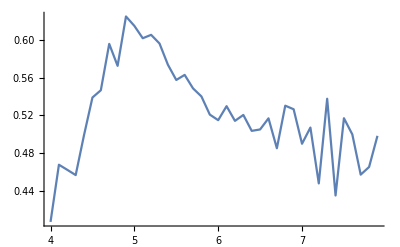

```mathematica
ListPlot[result,Joined->True]
```

Baseline

```mathematica
communities0=FindGraphPartition[g,5];
```

```mathematica
(*communities0=FindGraphCommunities[g];*)
```

```mathematica
purity[communities0,top5]
```

0.567999

use spectral method

```mathematica
(*adjancy=1/communityDistanceMatrix;
Table[adjancy[[i,i]]=0,{i,Length@adjancy}];
k=DiagonalMatrix@(Total/@adjancy);
m=Total@Flatten[k];*)
```